

```mathematica
Plot[x,{x,-2,2}]
```

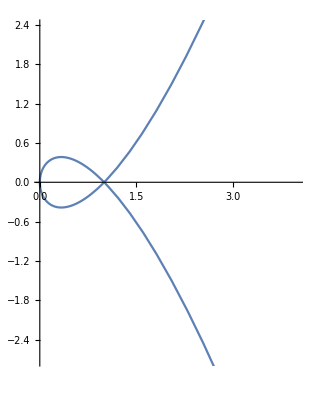

```mathematica
ParametricPlot[
{t^2,t(t^2-1)}
,{t,-2,2}]
```

```mathematica
Integrate[Norm[D[{t^2,t(t^2-1)},t]]^2,{t,0,1}]
```

32/15

```mathematica
N[32/15]
```

2.13333

```mathematica
Manipulate[
Show[{
ParametricPlot[
{t^2,t(t^2-1)}
,{t,-2,2}],
ParametricPlot[
{t^2,t(t^2-1)}
,{t,0,a}]
}],{a,0,1}]
```

ParametricPlot::plld: Endpoints for t in {t,0,FE`a$$23} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{,ParametricPlot[{t^2,t (t^2-1)},{t,0,FE`a$$23}]}].

ParametricPlot::plld: Endpoints for t in {t,0,FE`a$$23} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{,ParametricPlot[{t^2,t (t^2-1)},{t,0,FE`a$$23}]}].

```mathematica
Manipulate[
Show[{
ParametricPlot[
{t^2,t(t^2-1)}
,{t,0,a}],
ParametricPlot[
{t^2,t(t^2-1)}
,{t,-2,2}]
}],{a,0,1}]
```

ParametricPlot::plld: Endpoints for t in {t,0,FE`a$$31} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ParametricPlot[{t^2,t (t^2-1)},{t,0,FE`a$$31}],}].

ParametricPlot::plld: Endpoints for t in {t,0,FE`a$$31} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ParametricPlot[{t^2,t (t^2-1)},{t,0,FE`a$$31}],}].

ParametricPlot::plld: Endpoints for t in {t,0,FE`a$$31} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ParametricPlot[{t^2,t (t^2-1)},{t,0,FE`a$$31}],}].

```mathematica
Manipulate[
Show[{
ParametricPlot[
{t^2,t(t^2-1)}
,{t,0.01,a}],
ParametricPlot[
{t^2,t(t^2-1)}
,{t,-2,2}]
}],{a,0,1}]
```

```mathematica
Manipulate[
Show[{
ParametricPlot[
{t^2,t(t^2-1)}
,{t,0.01,a},PlotRange->{{-2,2},{-2,2}}],
ParametricPlot[
{t^2,t(t^2-1)}
,{t,-2,2},PlotRange->{{-2,2},{-2,2}}]
}],{a,0,1}]
```

```mathematica
Inactivate[Integrate[Norm[D[{t^2,t(t^2-1)},t]]^2,{t,0,1}]]
```

Norm[Inactive{t^2,t*(t^2+-1)}t]^2t01

```mathematica
1/2 Integrate[Norm[D[{t^2,t(t^2-1)},t]]^2,{t,0,1}]
```

16/15

```mathematica
N[16/15]
```

1.06667